```mathematica
eq={u u + v v + w w==1,u v ==F,u w==G};sol=Solve[eq,{u,v,w}];
```

```mathematica
uvw2={u u,v v, w w}/.sol
```

{{1/2 (1-√(1-4 F^2-4 G^2)),1/4 (-(F √(1-√(1-4 F^2-4 G^2)))/(√2 (F^2+G^2))-(F √(1-4 F^2-4 G^2) √(1-√(1-4 F^2-4 G^2)))/(√2 (F^2+G^2)))^2,((-(G √(1-√(1-4 F^2-4 G^2)))/(2 √2)-(G √(1-4 F^2-4 G^2) √(1-√(1-4 F^2-4 G^2)))/(2 √2))^2)/((F^2+G^2)^2)},{1/2 (1-√(1-4 F^2-4 G^2)),1/4 ((F √(1-√(1-4 F^2-4 G^2)))/(√2 (F^2+G^2))+(F √(1-4 F^2-4 G^2) √(1-√(1-4 F^2-4 G^2)))/(√2 (F^2+G^2)))^2,(((G √(1-√(1-4 F^2-4 G^2)))/(2 √2)+(G √(1-4 F^2-4 G^2) √(1-√(1-4 F^2-4 G^2)))/(2 √2))^2)/((F^2+G^2)^2)},{1/2+1/2 √(1-4 F^2-4 G^2),1/4 ((F √(1/2+1/2 √(1-4 F^2-4 G^2)))/(F^2+G^2)-(F √(1-4 F^2-4 G^2) √(1/2+1/2 √(1-4 F^2-4 G^2)))/(F^2+G^2))^2,((1/2 G √(1/2+1/2 √(1-4 F^2-4 G^2))-1/2 G √(1-4 F^2-4 G^2) √(1/2+1/2 √(1-4 F^2-4 G^2)))^2)/((F^2+G^2)^2)},{1/2+1/2 √(1-4 F^2-4 G^2),1/4 (-(F √(1/2+1/2 √(1-4 F^2-4 G^2)))/(F^2+G^2)+(F √(1-4 F^2-4 G^2) √(1/2+1/2 √(1-4 F^2-4 G^2)))/(F^2+G^2))^2,((-1/2 G √(1/2+1/2 √(1-4 F^2-4 G^2))+1/2 G √(1-4 F^2-4 G^2) √(1/2+1/2 √(1-4 F^2-4 G^2)))^2)/((F^2+G^2)^2)}}

```mathematica
FullSimplify[D[uvw2,F]]
```

{{(2 F)/(√(1-4 F^2-4 G^2)),(F (-2 F^4-6 F^2 G^2+G^2 (1-4 G^2+√(1-4 F^2-4 G^2))))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2),-(F G^2 (1-2 F^2-2 G^2+√(1-4 F^2-4 G^2)))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2)},{(2 F)/(√(1-4 F^2-4 G^2)),(F (-2 F^4-6 F^2 G^2+G^2 (1-4 G^2+√(1-4 F^2-4 G^2))))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2),-(F G^2 (1-2 F^2-2 G^2+√(1-4 F^2-4 G^2)))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2)},{-(2 F)/(√(1-4 F^2-4 G^2)),(F (2 F^4+6 F^2 G^2+G^2 (-1+4 G^2+√(1-4 F^2-4 G^2))))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2),-(F G^2 (-1+2 F^2+2 G^2+√(1-4 F^2-4 G^2)))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2)},{-(2 F)/(√(1-4 F^2-4 G^2)),(F (2 F^4+6 F^2 G^2+G^2 (-1+4 G^2+√(1-4 F^2-4 G^2))))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2),-(F G^2 (-1+2 F^2+2 G^2+√(1-4 F^2-4 G^2)))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2)}}

```mathematica
FullSimplify[D[uvw2,G]]
```

{{(2 G)/(√(1-4 F^2-4 G^2)),-(F^2 G (1+√(1-4 F^2-4 G^2))^2)/(2 √(1-4 F^2-4 G^2) (F^2+G^2)^2),(G (-4 F^4-2 G^4+F^2 (1-6 G^2+√(1-4 F^2-4 G^2))))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2)},{(2 G)/(√(1-4 F^2-4 G^2)),-(F^2 G (1+√(1-4 F^2-4 G^2))^2)/(2 √(1-4 F^2-4 G^2) (F^2+G^2)^2),(G (-4 F^4-2 G^4+F^2 (1-6 G^2+√(1-4 F^2-4 G^2))))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2)},{-(2 G)/(√(1-4 F^2-4 G^2)),(F^2 G (-1+√(1-4 F^2-4 G^2))^2)/(2 √(1-4 F^2-4 G^2) (F^2+G^2)^2),(G (4 F^4+2 G^4+F^2 (-1+6 G^2+√(1-4 F^2-4 G^2))))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2)},{-(2 G)/(√(1-4 F^2-4 G^2)),(F^2 G (-1+√(1-4 F^2-4 G^2))^2)/(2 √(1-4 F^2-4 G^2) (F^2+G^2)^2),(G (4 F^4+2 G^4+F^2 (-1+6 G^2+√(1-4 F^2-4 G^2))))/(√(1-4 F^2-4 G^2) (F^2+G^2)^2)}}

```mathematica
EE=((en-mu)^2+Dt^2)^(1/2);ff=Dt/(2EE)
```

Dt/(2 √(Dt^2+(en-mu)^2))

```mathematica
bec={mu->-10,Dt->2};bcs={mu->10,Dt->0.2}
```

{mu→10,Dt→0.2}

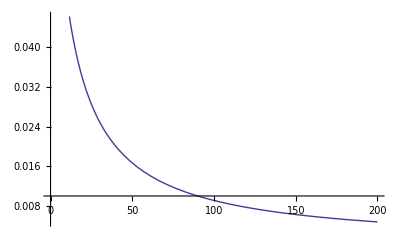

```mathematica
Plot[ff/.bec,{en,0,200}]
```

```mathematica
ff/.bcs
```

ReplaceAll::reps: {bcs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Dt/(2 √(Dt^2+(en-mu)^2))/.bcs